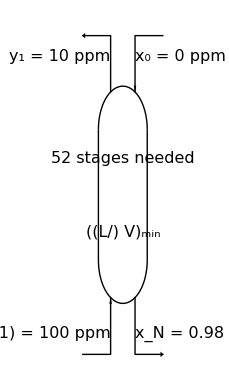

```mathematica
Module[{h,w,ry,x1,x2,yt1,yt2,yb1,yb2},
h=10;w=15;ry=2;
x1=-5;x2=w-x1;
(*yt1=13.33;yt2=9.7;yb1=-4.6;yb2=0.28;*)
(*yt1=12.33;yt2=9.7;yb1=yb2-(yt1-yt2);yb2=0.3;*)
yt1=h+h/4.3;yt2=h/1.03;yb1=h-h/0.81;yb2=0.03*h;

Graphics[{Thick,
Line[{{#,ry},{#,h-ry}}]&/@{0,w},Circle[{w/2,ry},{w/2,ry},{π,2*π}],Circle[{w/2,h-ry},{w/2,ry},{0,π}],
(*****************)
Text[Style["52 stages needed",16],{0.5*w,0.666*h}],
Text[Style[Subscript[Row@{"(",Style["L",Italic],"/",Style["V",Italic]")"},"min"],16],{0.5*w,0.33*h}],

Arrowheads@0.1,
Arrow[{{0.25*w,yt2},{0.25*w,yt1},{x1,yt1}}],
Arrow[{{x1,yb1},{0.25*w,yb1},{0.25*w,yb2}}],
Arrow[{{x2,yt1},{0.75*w,yt1},{0.75*w,yt2}}],
Arrow[{{0.75*w,yb2},{0.75*w,yb1},{x2,yb1}}],

Text[Style["y_1 = 10 ppm",16,Background->White],{0.25*w,(yt1+yt2)/2},{0.5,-0.5}],
Text[Style["y_(N + 1) = 100 ppm",16,Background->White],{0.25*w,(yb1+yb2)/2},{0.5,0.5}],
Text[Style["x_0 = 0 ppm",16,Background->White],{0.75*w,(yt1+yt2)/2},{-0.5,-0.5}],
Text[Style["x_N = 0.98 ppm",16,Background->White],{0.75*w,(yb1+yb2)/2},{-0.5,0.5}],

},ImageSize->{230,390},AspectRatio->Full,PlotRangePadding->{None,Scaled@0.01}]
]
```

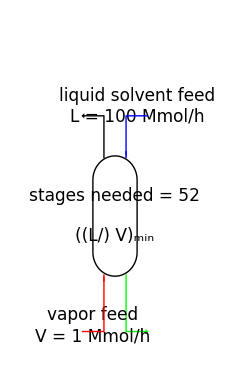

```mathematica
Module[{h,w,ry},
h=10;w=10;ry=2;

Graphics[{
Thick,
Line[{{#,ry},{#,h-ry}}]&/@{0,w},Circle[{w/2,ry},{w/2,ry},{π,2*π}],Circle[{w/2,h-ry},{w/2,ry},{0,π}],
(***********)

Text[Style["stages needed = 52",17],{0.5*w,0.666*h}],
Text[Style[Subscript[Row@{"(",Style["L",Italic],"/",Style["V",Italic]")"},"min"],17],{0.5*w,0.33*h}],

Text[Style[Column[{"liquid solvent feed",Row@{Style["L",Italic]," = 100 Mmol/h"}},Right],17],{w,h+h/4},{0.2,-1.2}],
Text[Style[Column[{"vapor feed",Row@{Style["V",Italic]," = 1 Mmol/h"}}],17],{0,-h/4},{0,1.4}],

Arrowheads@0.1,
{Arrow[{{0.25*w,h/1.02},{0.25*w,#},{-w/4,#}}],Blue,Arrow[{{w+w/4,#1},{0.75*w,#1},{0.75*w,h/1.02}}]}&@(h+h/3),
{Red,Arrow[{{-w/4,#},{0.25*w,#},{0.25*w,0.015*h}}],Green,Arrow[{{0.75*w,0.015*h},{0.75*w,#},{w+w/4,#}}]}&@(-4.6)

},ImageSize->{230,390},AspectRatio->Full,PlotRange->{-6.5,20}]
]
```

```mathematica
N@13/0.2
```

65.

```mathematica
0.2/13
```

0.0153846

```mathematica
N@(13+13/3-12.73)
```

4.60333

```mathematica
Reverse@{{0.75*w,12.73},{0.75*w,#},{w+w/4,#}}
```

{{(5 w)/4,#1},{0.75 w,#1},{0.75 w,12.73}}

```mathematica
N@13/12.73
```

1.02121